# Periodic Sequences in 1D

This is all much easier in 1D.  For a function f:ℝ→ℝ  consider the sequence defined recursively by 
	p_(n+1)=f(p_n)
and an initial value p_0∈ℝ. We will make smoothness assumptions about f as we need them.  Lets look at an example.

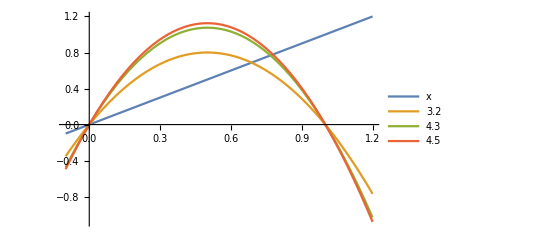

```mathematica
f[r_][x_]:= r x (1-x)
rs={3.2,4.3,4.5};
fs=Join[{x},Table[f[r][x],{r,rs}]];
Plot[fs,{x, -0.1,1.2},
PlotLegends->Join[{"x"},rs]]
```

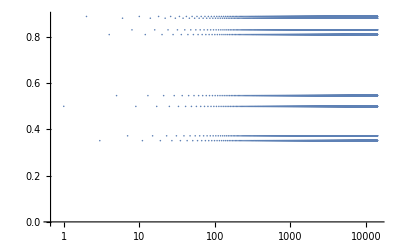

```mathematica
MaxIter=14200;
x0=0.5;
r=3.555;
Data=NestList[f[r],x0,MaxIter];
ListLogLinearPlot[Data,
PlotRange->All,
Joined->False,
GridLines->Automatic]
```

Here is a rather famous picture of all of this behavior.

```mathematica
x0=0.2;
MaxIter=1250;
rData=Partition[
Flatten[Table[
Data=NestList[f[r], x0, MaxIter]⟦Floor[MaxIter/2];;-1⟧;
Table[ {r,Data⟦i⟧},{i, Length[Data]}],
{r,2.5,4,0.001}]],2];
ListPlot[rData,
Frame->True,
FrameLabel->{"r","x"},
GridLines->Automatic]
```

-Graphics-

```mathematica
x0=0.2;
MaxIter=1250;
rData=Partition[
Flatten[Table[
Data=NestList[f[r], x0, MaxIter]⟦Floor[MaxIter/2];;-1⟧;
Table[ {r,Data⟦i⟧},{i, Length[Data]}],
{r,3.54,3.6,0.00005}]],2];
ListPlot[rData,
Frame->True,
FrameLabel->{"r","x"},
GridLines->Automatic]
```

-Graphics-

Lets see if we can find these values.

```mathematica
Clear[r]
Solve[f[r][x]==x,x]
Solve[Nest[f[r],x,2]==x,x]
```

{{x→0},{x→(-1+r)/r}}

{{x→0},{x→(-1+r)/r},{x→(r+r^2-r √(-3-2 r+r^2))/(2 r^2)},{x→(r+r^2+r √(-3-2 r+r^2))/(2 r^2)}}

```mathematica
Solve[ -3-2 r+r^2==0,r]
```

{{r→-1},{r→3}}

```mathematica
Plot3D[{x,f[r][f[r][x]]},{r,2,4.5},{x,0,1},
AxesLabel->{"r","x","z"},
PlotPoints->50]
```

```mathematica
Plot3D[{x,Nest[f[r],x,2]},{r,2,4.5},{x,0,1},
AxesLabel->{"r","x","z"},
PlotPoints->50]
```

-Graphics3D-

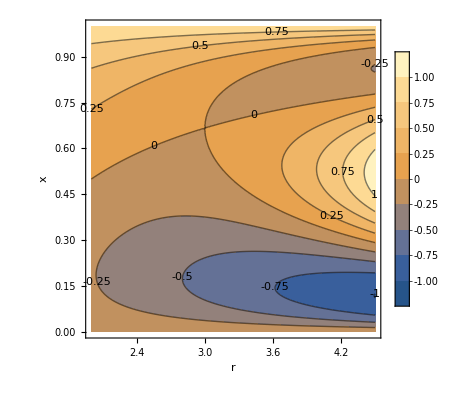

```mathematica
ContourPlot[x-Nest[f[r],x,2],{r,2,4.5},{x,0,1},
FrameLabel->{"r","x"},
PlotPoints->50,
ContourLabels->True,
PlotLegends->Automatic]
```

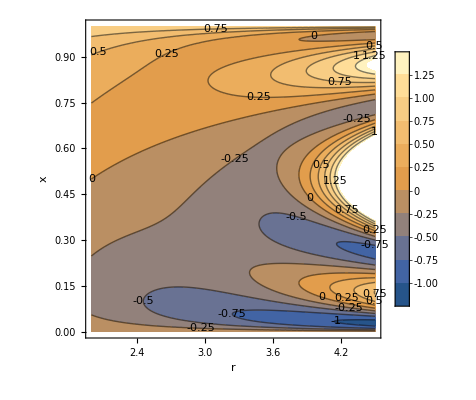

```mathematica
ContourPlot[x-Nest[f[r],x,3],{r,2,4.5},{x,0,1},
FrameLabel->{"r","x"},
PlotPoints->50,
ContourLabels->True,
PlotLegends->Automatic]
```

```mathematica
ContourPlot[x-Nest[f[r],x,4],{r,2,4.5},{x,0,1},
FrameLabel->{"r","x"},
PlotPoints->50,
ContourLabels->True,
PlotLegends->Automatic]
```

-Graphics-

```mathematica
ContourPlot[x-Nest[f[r],x,5],{r,3.5,4.5},{x,0,1},
FrameLabel->{"r","x"},
PlotPoints->50,
ContourLabels->True,
PlotLegends->Automatic]
```

-Graphics-

```mathematica
ContourPlot[x-Nest[f[r],x,6],{r,3.5,4.5},{x,0.8,1},
FrameLabel->{"r","x"},
PlotPoints->50,
ContourLabels->True,
PlotLegends->Automatic]
```

-Graphics-

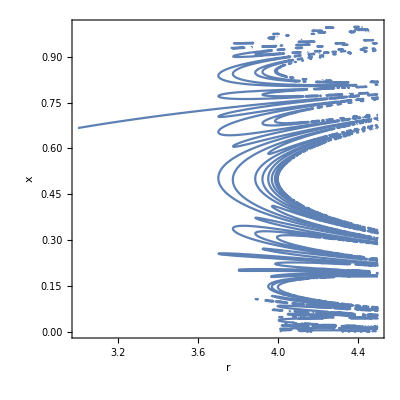

```mathematica
ContourPlot[x-Nest[f[r],x,7]==0,{r,3,4.5},{x,0,1},
FrameLabel->{"r","x"},
PlotPoints->50,
ContourLabels->True,
PlotLegends->Automatic]
```

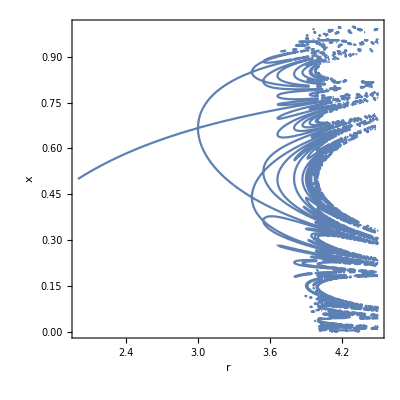

```mathematica
ContourPlot[x-Nest[f[r],x,8]==0,{r,2,4.5},{x,0,1},
FrameLabel->{"r","x"},
PlotPoints->50,
ContourLabels->True,
PlotLegends->Automatic]
```

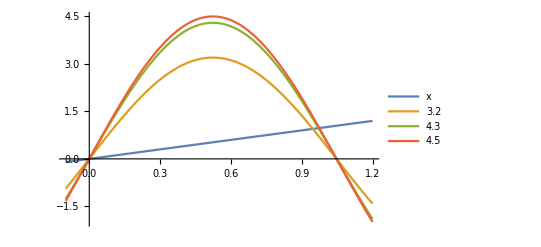

```mathematica
f[r_][x_]:= r Sin[3x]
rs={3.2,4.3,4.5};
fs=Join[{x},Table[f[r][x],{r,rs}]];
Plot[fs,{x, -0.1,1.2},
PlotLegends->Join[{"x"},rs]]
```

```mathematica
x0=0.2;
MaxIter=1250;
rData=Partition[
Flatten[Table[
Data=NestList[f[r], x0, MaxIter]⟦Floor[MaxIter/2];;-1⟧;
Table[ {r,Data⟦i⟧},{i, Length[Data]}],
{r,0.5,1.1,0.001}]],2];
ListPlot[rData,
Frame->True,
FrameLabel->{"r","x"},
GridLines->Automatic]
```

-Graphics-